# Read Latency Comparison: 2AM vs. RWN

## 2016-04-07 hengxin0912@gmail.com File: “~/mma-projects/RWN-latency/rwn-2am-read-latency.nb Online: github???

```mathematica
ClearAll[latencyDir,rawLatencyDataRelativeDir,rawLatencyDataFullDir];
```

## Directory:

```mathematica
latencyDir="~/mma-projects/2am/RWN-latency/";
rawLatencyDataRelativeDir="rwn-latency-raw-data/";
rawLatencyDataFullDir=latencyDir<>rawLatencyDataRelativeDir;
SetDirectory[rawLatencyDataFullDir];
```

## Data Import:

```mathematica
dataImport[file_String]:=
Module[{data},
data=Select[Import[file,"Table"], First[#]==1&][[All,2]]
];
```

## Quantiles:

```mathematica
quantiles[data_List]:=
Module[{},
Append[Quantile[data,{0,0.25,0.5,0.75,0.95,0.99,1.0},{{1/2,0},{0,1}}],Round[Mean[data]]]
];
```

## Quantiles for all RWN Executions:

```mathematica
quantilesAll=quantiles[dataImport[rawLatencyDataFullDir<>#]]&/@FileNames[];
```

## Export Data:

```mathematica
Export[latencyDir<>"rwn-2am-read-latency-quantiles.txt",quantilesAll, "Table"]
```

~/mma-projects/2am/RWN-latency/rwn-2am-read-latency-quantiles.txt

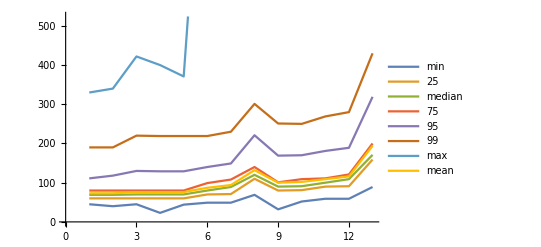

```mathematica
ListLinePlot[Transpose[quantilesAll],PlotLegends->{"min","25","median", "75","95","99", "max","mean"}]
```

## The remaining work is done with PGFPlots.

### See

```mathematica
FileNames[]
```

{1+1less3-delay.txt,1+2equal3-delay.txt,1+2less5-delay.txt,1+3less5-delay.txt,1+4equal5-delay.txt,2+1equal3-delay.txt,2+2greater3-2atomicity-latency.txt,2+2greater3-atomicity-latency.txt,2+2less5-latency.txt,2+3equal5-delay.txt,3+2equal5-delay.txt,3+3greater5-2atomicity-latency.txt,3+3greater5-atomicity-delay.txt}